### Taking advantage of class-4 mean difference after many steps

```mathematica
BlockMap[f, {1, 2, 3}, 2, 1]
```

{f[{1,2}],f[{2,3}]}

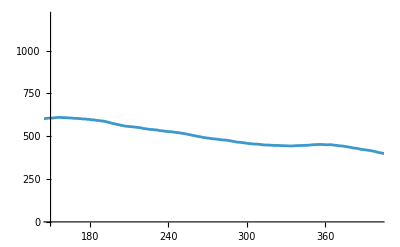

```mathematica
ListLinePlot[BlockMap[Mean,Total/@CellularAutomaton[{1815,{3,1}},RandomInteger[2,1200],1490], 50, 1], PlotRange->{{150, 400}, {0, 1200}}]
```

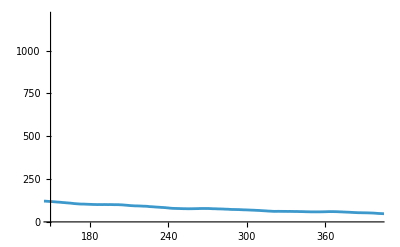

```mathematica
ListLinePlot[BlockMap[Mean,Total/@CellularAutomaton[{1815,{3,1}},RandomInteger[2,200],1490], 50, 1], PlotRange->{{150, 400}, {0, 1200}}]
```

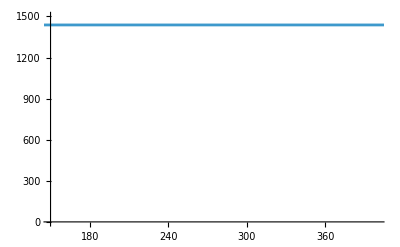
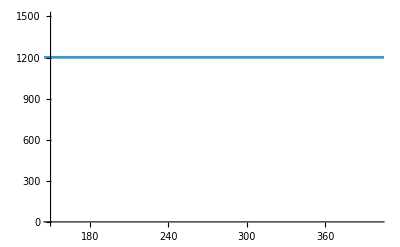
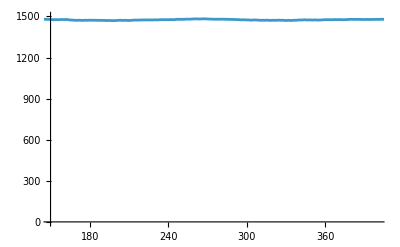
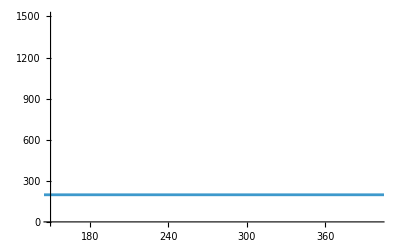
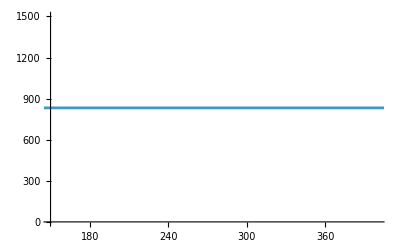
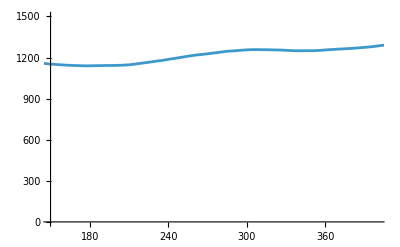
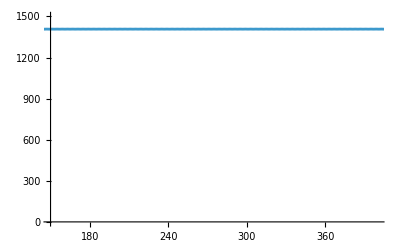
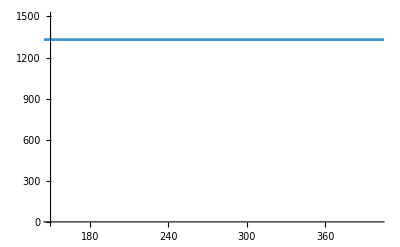

```mathematica
Table[ListLinePlot[BlockMap[Mean,Total/@CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"],3, 1},RandomInteger[2,1200],1490], 50, 1], PlotRange->{{150, 400}, {0, 1500}}], 10]
```

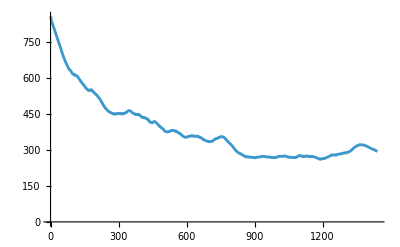

```mathematica
ListLinePlot[BlockMap[Mean,Total/@CellularAutomaton[{1815,{3,1}},RandomInteger[2,1200],1490], 50, 1]]
```

```mathematica
rfs = Module[{width = 1200, length  = 400},
ParallelMap[With[{tots = Total/@CellularAutomaton[#, RandomInteger[1, width], {{150, 400}}]}, Append[#, "fitness"->N@Abs[Mean[tots[[-50;;]]] - Mean[tots[[;;50]]]]]]&, Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 10000]]];
```

```mathematica
ByteCount[rfs]
```

7120080

```mathematica
Iconize[rfs]
```

```mathematica
rfs = ;
```

```mathematica
GraphicsRow[{Rasterize[ArrayPlot[#]], ListLinePlot[Total/@ #, PlotHighlighting->None], ListLinePlot[Differences[Total/@ #], PlotHighlighting->None, PlotRange->All], Histogram[Differences[Total/@ #]]}]&[CellularAutomaton[{#RuleNumber, 2, 2},RandomInteger[1,500],400]]&/@ReverseSortBy[rfs, #fitness&][[;;30]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 2, 2},RandomInteger[1,500],400]], #fitness]&/@ReverseSortBy[rfs, #fitness&][[240;;270]]
```

{-Graphics-34.64,-Graphics-34.62,-Graphics-34.62,-Graphics-34.6,-Graphics-34.56,-Graphics-34.54,-Graphics-34.54,-Graphics-34.48,-Graphics-34.26,-Graphics-34.16,-Graphics-34.16,-Graphics-33.74,-Graphics-33.56,-Graphics-33.44,-Graphics-33.34,-Graphics-33.26,-Graphics-33.04,-Graphics-33.02,-Graphics-32.94,-Graphics-32.82,-Graphics-32.62,-Graphics-32.52,-Graphics-32.42,-Graphics-32.42,-Graphics-32.26,-Graphics-32.22,-Graphics-32.2,-Graphics-32.08,-Graphics-31.96,-Graphics-31.84,-Graphics-31.76}

#### Bottom rules

```mathematica
GraphicsRow[{Rasterize[ArrayPlot[#]], ListLinePlot[Total/@ #, PlotHighlighting->None], ListLinePlot[Differences[Total/@ #], PlotHighlighting->None, PlotRange->All], Histogram[Differences[Total/@ #]]}]&[CellularAutomaton[{#RuleNumber, 2, 2},RandomInteger[1,500],400]]&/@SortBy[rfs, #fitness&][[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Distribution of “bubbling” metric

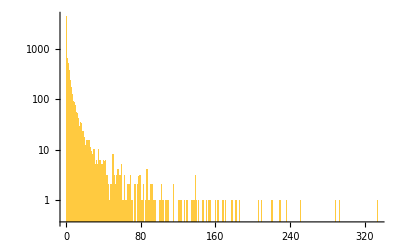

```mathematica
Histogram[rfs[[All, "fitness"]], PlotRange->All, ScalingFunctions->"Log"]
```

### Trying for more colors

```mathematica
rfs = Module[{width = 1200, length  = 400},
ParallelMap[With[{tots = Total/@CellularAutomaton[#, RandomInteger[1, width], {{150, 400}}]}, Append[#, "fitness"->N@Abs[Mean[tots[[-50;;]]] - Mean[tots[[;;50]]]]]]&, Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 10000]]];
```

```mathematica
ByteCount[rfs]
```

7120080

```mathematica
GraphicsRow[{Rasterize[ArrayPlot[#]], ListLinePlot[Total/@ #, PlotHighlighting->None], ListLinePlot[Differences[Total/@ #], PlotHighlighting->None, PlotRange->All], Histogram[Differences[Total/@ #]]}]&[CellularAutomaton[{#RuleNumber, 2, 2},RandomInteger[1,500],400]]&/@ReverseSortBy[rfs, #fitness&][[;;30]]
```

### Mapping one density to another

### Langton’s number?